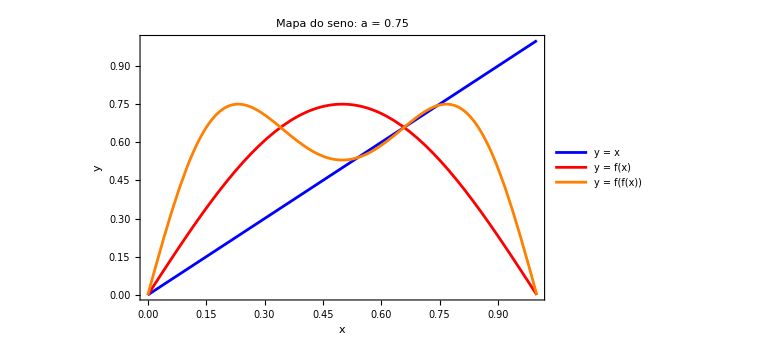

{{x→0.},{x→0.6587}}

x* | |f'(x*)|
0. | 2.35619
0.6587 | 1.12666

General::munfl: 0.001 4.49039×10^-306 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.002 8.85113×10^-307 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.003 1.30297×10^-306 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

-Graphics-

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal, but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

Periodo | a critico
2 | 0.833266
4 | 0.858609
8 | 0.890386
16 | 0.913432
32 | 0.931458
64 | 0.946005
128 | 0.957254

j | delta_j | Erro
3 | 0.797531 | 3.87167
4 | 1.37879 | 3.29041
5 | 1.27857 | 3.39063
6 | 1.23905 | 3.43015
7 | 1.29325 | 3.37595

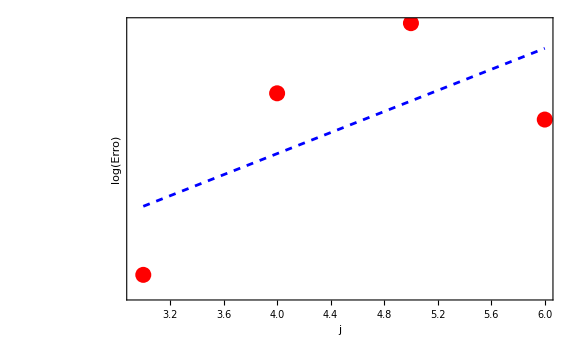

0.690199

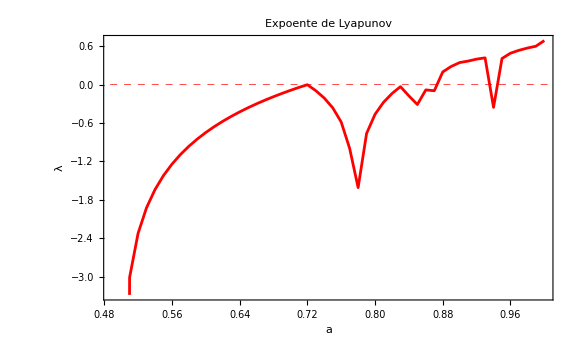

```mathematica
(*PROBLEMA 1:MAPA DO SENO*)


(*Configuracoes*)
optam={ImageSize->Large,LabelStyle->"Medium"};

(*------------------------------------------------------------------------*)
(*Item 1.1:Analise para a=0.75*)


(*Definir o mapa*)
g[x_]:=0.75*Sin[Pi*x]

(*Segunda iteracao*)
g2[x_]:=g[g[x]]

(*Grafico*)
grafico1=Plot[{x,g[x],g2[x]},{x,0,1},PlotStyle->{Blue,Red,Orange},PlotLegends->{"y = x","y = f(x)","y = f(f(x))"},Frame->True,FrameLabel->{"x","y"},PlotLabel->"Mapa do seno: a = 0.75",Evaluate[optam]]

(*Encontrar pontos fixos*)
solPF=NSolve[x==g[x]&&0<=x<=1,x,Reals]

(*Derivada*)
glin[x_]:=0.75*Pi*Cos[Pi*x]

(*Estabilidade*)
estab=Table[{x/. solPF[[i]],Abs[glin[x/. solPF[[i]]]]},{i,Length[solPF]}];
Grid[Prepend[estab,{"x*","|f'(x*)|"}],Frame->All]

(*------------------------------------------------------------------------*)
(*Item 1.2:Diagrama de bifurcacoes*)


(*Redefinir g com parametro a*)
Clear[g];
g[a_,x_]:=a*Sin[Pi*x]

(*Iterar e coletar pontos-maior resolucao*)
pontosDiag=Flatten[Table[Module[{x=0.5,lista},Do[x=g[a,x],{1000}];(*transiente maior*)lista=Table[x=g[a,x];{a,x},{1000}];(*mais pontos*)lista],{a,0.,1.,0.001} (*passo menor*)],1];

(*Plotar diagrama*)
diag1=ListPlot[pontosDiag,PlotStyle->{PointSize[0.001],Red},Frame->True,FrameLabel->{"a","x"},PlotLabel->"Diagrama de Bifurcacoes",AspectRatio->1,Evaluate[optam]]

(*------------------------------------------------------------------------*)
(*Item 1.3:Valores criticos de a*)


(*Funcao auxiliar para n-esima iteracao*)
gn[a_,x_,n_]:=Nest[g[a,#]&,x,n]

(*Encontrar primeira bifurcacao*)
sol2=FindRoot[{x==gn[a,x,2],Abs[D[gn[a,y,2],y]/. y->x]==1},{{a,0.72},{x,0.4}}];
avals={a/. sol2};

(*Proximas bifurcacoes*)
Do[Module[{aguess=avals[[-1]]+(1-avals[[-1]])/4.8,sol},sol=FindRoot[{x==gn[a,x,2^k],Abs[D[gn[a,y,2^k],y]/. y->x]==1},{{a,aguess},{x,0.5}},MaxIterations->100];
AppendTo[avals,a/. sol]],{k,2,7}];

(*Tabela*)
tabBif=Table[{2^k,avals[[k]]},{k,Length[avals]}];
Grid[Prepend[tabBif,{"Periodo","a critico"}],Frame->All]

(*------------------------------------------------------------------------*)
(*Item 1.4:Constante de Feigenbaum*)


deltas=Table[(avals[[j]]-avals[[j-1]])/(avals[[j+1]]-avals[[j]]),{j,2,Length[avals]-1}];

deltaTeor=4.669201609;

tabDelta=Table[{j+1,deltas[[j-1]],Abs[deltas[[j-1]]-deltaTeor]},{j,2,Min[6,Length[deltas]+1]}];
Grid[Prepend[tabDelta,{"j","delta_j","Erro"}],Frame->All]

(*------------------------------------------------------------------------*)
(*Item 1.5:Ajuste exponencial*)

dados=Table[{j,Abs[deltas[[j-1]]-deltaTeor]},{j,3,Min[6,Length[deltas]+1]}];

ajuste=NonlinearModelFit[dados,c1*Exp[-c2*j],{c1,c2},j];

Show[ListLogPlot[dados,PlotStyle->{Red,PointSize[0.02]}],LogPlot[ajuste[j],{j,3,6},PlotStyle->{Blue,Dashed}],Frame->True,FrameLabel->{"j","log(Erro)"},Evaluate[optam]]

(*------------------------------------------------------------------------*)
(*Item 1.6:Expoente de Lyapunov*)

lyap[a_,x0_,niter_,ntrans_]:=Module[{x=x0,soma=0.},Do[x=g[a,x],{ntrans}];
Do[soma+=Log[Abs[a*Pi*Cos[Pi*x]]];
x=g[a,x],{niter}];
soma/niter]

(*Para a=1*)
lyap[1.0,0.5,10000,1000]

(*Grafico*)
dadosLyap=Table[{a,lyap[a,0.5,5000,500]},{a,0.5,1.0,0.01}];

ListPlot[dadosLyap,Joined->True,Frame->True,FrameLabel->{"a","λ"},PlotLabel->"Expoente de Lyapunov",GridLines->{{},{0}},GridLinesStyle->Directive[Red,Dashed],PlotStyle->Red,Evaluate[optam]]
(*Exponente de Lyapunov positivo denota o comportamento caótico,dessa maneira, o comportamento caótico pode ser visot em a=0.720 e na maior parte do intervalo a=~[0.875,1]*)
```